## Parameters

1. DE with w=-1 ~ LCDM

w=-1;
Ω_DE0=0.734;
Ω_k0=0;
Ω_m0=0.1334/(0.71^2);
Ω_r0=8.09*10^-5;
H_0=71/300000;

## DE & LCDM & sCDM

Hubble distance

```mathematica
w=-1;
Subscript[Ω, DE0]=0.734;
Subscript[Ω, k0]=0;
Subscript[Ω, m0]=0.1334/(0.71^2);
Subscript[Ω, r0]=8.09*10^-5;
Subscript[H, 0]=71/300000;
H[a_]:=Subscript[H, 0] √(Subscript[Ω, m0] a^-3+Subscript[Ω, r0] a^-4+Subscript[Ω, DE0] a^(-3(1+w)));
Subscript[d, H]=1/H[a]
1/NIntegrate[1/(x^2 H[x]),{x,0,a}]
```

Growth function

```mathematica
Subscript[w, 1]=-1;
Subscript[w, 2]=-0.5;
Subscript[Ω, DE0]=0.734;
Subscript[Ω, k0]=0;
Subscript[Ω, m0]=0.1334/(0.71^2);
Subscript[Ω, r0]=8.09*10^-5;
Subscript[H, 0]=71/300000;
Subscript[Ω, m0,s]=1;Subscript[Ω, r0,s]=8.09*10^-5;Subscript[H, 0]=71/300000;
Subscript[H, s][a_]:=Subscript[H, 0] √(Subscript[Ω, m0,s] a^-3+Subscript[Ω, r0,s] a^-4);
Subscript[H, L][a_]:=Subscript[H, 0] √(Subscript[Ω, m0] a^-3+Subscript[Ω, r0] a^-4+Subscript[Ω, DE0] a^(-3(1+Subscript[w, 1])))
Subscript[H, 2][a_]:=Subscript[H, 0] √(Subscript[Ω, m0] a^-3+Subscript[Ω, r0] a^-4+Subscript[Ω, DE0] a^(-3(1+Subscript[w, 2])))
Subscript[d, H,L][a]=1/(Subscript[H, L][a]);Subscript[d, H,2][a]=1/(Subscript[H, 2][a]);
kL[a_]=Subscript[H, L][a];Subscript[kL, 2][a_]=Subscript[H, 2][a];Subscript[k, s][a_]=Subscript[H, s][a];
(*ss[k_]:=NSolve[k==Subscript[H, 1][Subscript[a, 1]]&&Subscript[a, 1]>0,Subscript[a, 1]]//FullSimplify
Solve[k==Subscript[H, 2][Subscript[a, 2]],Subscript[a, 2]];*)
Subscript[Growth, s][a_]:= 5/2 Subscript[Ω, m0,s] (Subscript[H, s][a])/Subscript[H, 0]  NIntegrate[1/(x^3((Subscript[H, s][x])/Subscript[H, 0])^3),{x,0,a}];
GrowthL[a_]:= 5/2 Subscript[Ω, m0] (Subscript[H, L][a])/Subscript[H, 0]  NIntegrate[1/(x^3((Subscript[H, L][x])/Subscript[H, 0])^3),{x,0,a}];
Subscript[GrowthDE, 2][a_]:=5/2 Subscript[Ω, m0] (Subscript[H, 2][a])/Subscript[H, 0]  NIntegrate[1/(x^3((Subscript[H, 2][x])/Subscript[H, 0])^3),{x,0,a}];
(*k~a*)
LogPlot[{kL[a],Subscript[kDE, 2][a],Subscript[k, s][a]},{a,10^-3,1}];
(*eg*)
ParametricPlot[{Log[kL[a]],Log[GrowthL[1]/GrowthL[a]]},{a,10^-3,1},PlotRange->Full,AxesOrigin-> {-9,0}];
(*Growth~a*)
Plot[{GrowthL[a],Subscript[GrowthDE, 2][a],Subscript[Growth, s][a]},{a,0,1},PlotStyle->{Red,Green,Black},AxesLabel-> {a,"D_+(a)"}];
(*Growth with respect to 1+z*)
xyz[mn_]:=GrowthL[1/mn];rst[mn_]:=Subscript[GrowthDE, 2][1/mn];uvw[mn_]:=Subscript[Growth, s][1/mn];
LogLogPlot[{(mn)xyz[mn],(mn)rst[mn]},{mn,0.1,100},AxesLabel-> {"1+z","D_+(z)(1+z)"}];
(*The Q factor*)
(*DataList*)
PowerS=Import["E:\\KuaiPan\\MA_Lei\\PSLCDM.dat"];
PowerS[[1,1]]
Solve[PowerS[[1,1]]==Subscript[H, L][Subscript[a, L]],Subscript[a, L],Reals]
NSolve[PowerS[[1,1]]==Subscript[H, L][Subscript[a, L]],Subscript[a, L],Reals]
solL:=Solve[PowerS[[i,1]]==Subscript[H, L][Subscript[a, L]] && Subscript[a, L]>0,Subscript[a, L],Reals]
aokTabL=Table[Subscript[a, L]/.solL,{i,1,10}];
solDE2:=Solve[PowerS[[i,1]]==Subscript[H, L][Subscript[a, 2]] && Subscript[a, 2]>0,Subscript[a, 2],Reals]
aokTabDE2=Table[Subscript[a, 2]/.solDE2,{i,1,10}]
Qfactor=Table[{PowerS[[i,1]],((Subscript[GrowthDE, 2][1])/(Subscript[GrowthDE, 2][aokTabDE2[[i]][[1]]]))/(GrowthL[1]/GrowthL[aokTabL[[i]][[1]]])},{i,1,Length[PowerS]}]
ListLogLinearPlot[Qfactor,Joined->True, AxesLabel-> {k,Q},PlotRange->Full]
PowerSDE2=Table[{PowerS[[i,1]],((Subscript[GrowthDE, 2][1])/(Subscript[GrowthDE, 2][aokTabDE2[[i]][[1]]]))/(GrowthL[1]/GrowthL[aokTabL[[i]][[1]]])PowerS[[i,2]]},{i,1,Length[PowerS]}]
ListLogLinearPlot[PowerSDE2,Joined->True, AxesLabel-> {k,PowerSpectrum},PlotRange->Full]
(*Table[NSolve[PowerS[[i,1]]==Subscript[H, 2][Subscript[a, 2]] && Subscript[a, 2]>0,Subscript[a, 2],Reals],{i,1,Length[PowerS]}]*)
```

## Write Data to files.

Parameters

Intial conditions for Hubble constant, normalized to equality

0.0000809

0.00030571

0.0000165735

0.000236288

0.000236666

0.000236667

Define Hubble functions

Hubble distances

Define k of a

Define growth factors

Plot k of a

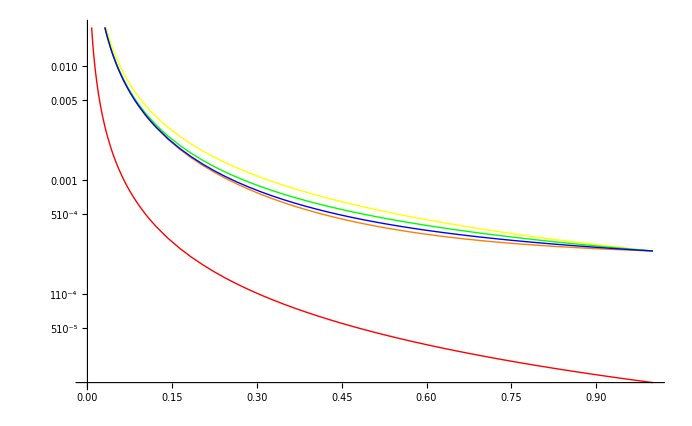

Plot growth factors of a for LCDM

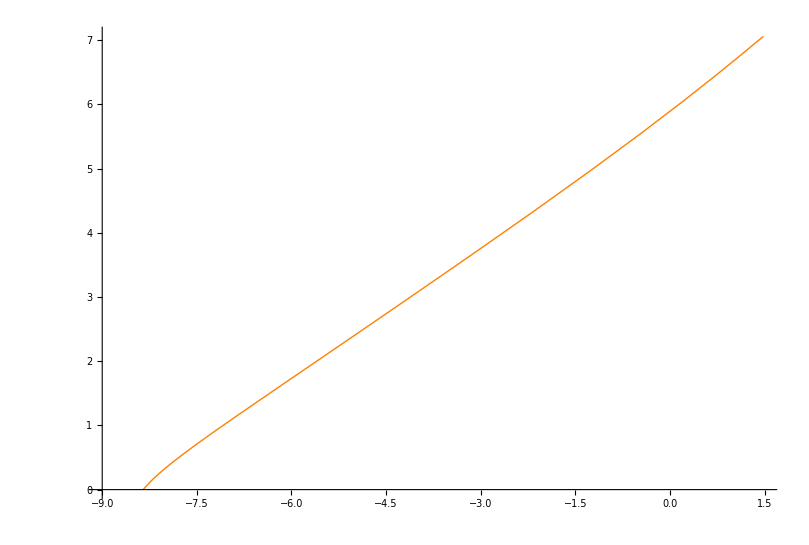

Plot growth factors of a for all models

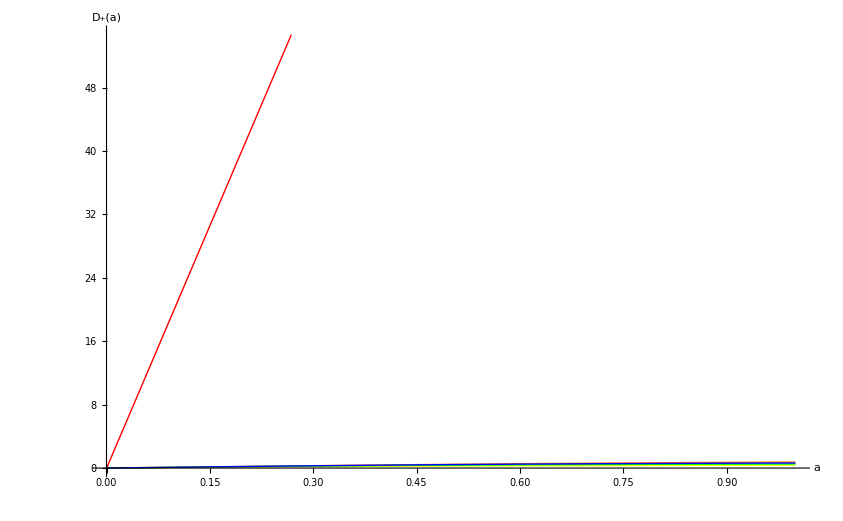

NIntegrate::nlim: x = a is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.7194}. NIntegrate obtained 41.459  + 55.5417\ ⅈ
 and 38.5744 for the integral and error estimates.

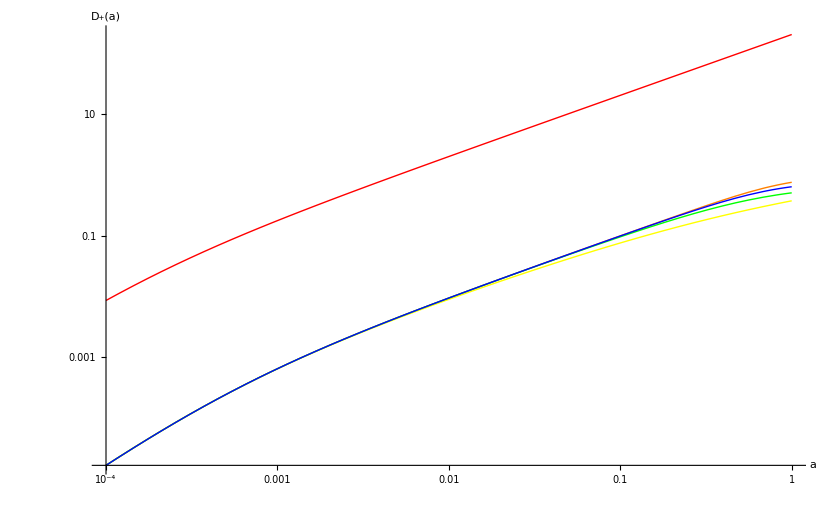

Tranform growth factors / Hubble distances of a to those of 1+z

Plot Hubble distances

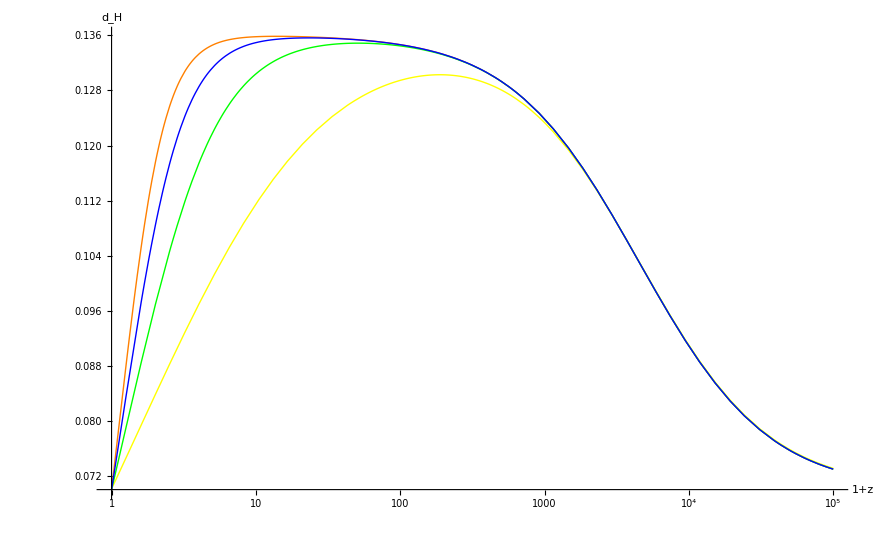

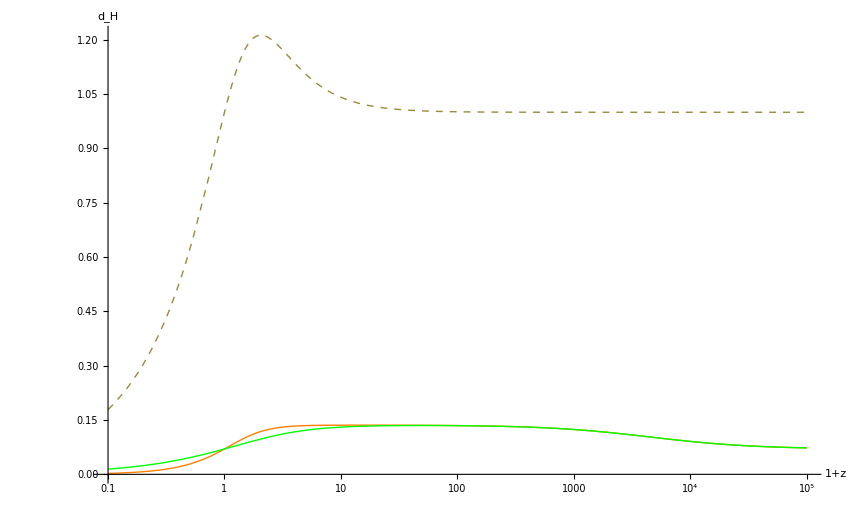

Plot growth factors in terms of 1+z

NIntegrate::nlim: x = 1/mn is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

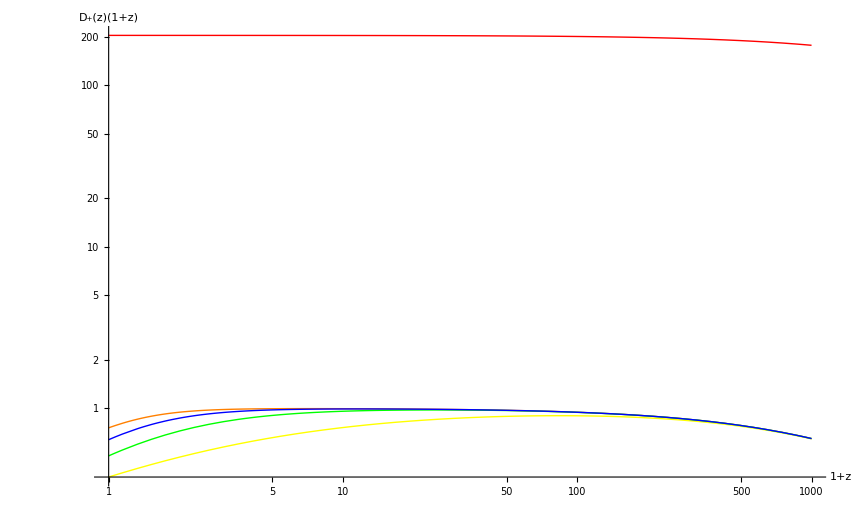

NIntegrate::nlim: x = 1/mn is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

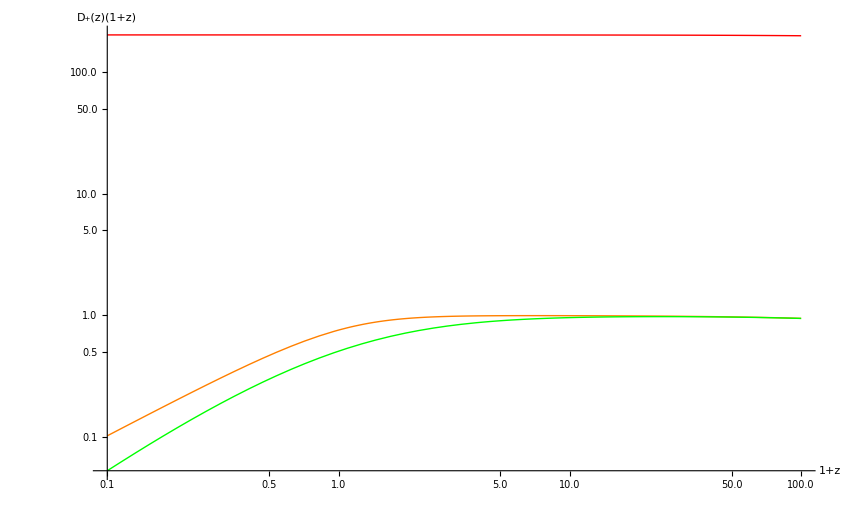

```mathematica
(*********************************************)
Print[Style["Parameters",Orange]]
(*********************************************)
Subscript[w, 1]=-1;
Subscript[w, 2]=-0.25;
Subscript[w, 3]=-0.5;
Subscript[w, 4]=-0.75;
Subscript[Ω, DE0]=0.734;
Subscript[Ω, k0]=0;
Subscript[Ω, m0]=0.1334/(0.71^2);
Subscript[Ω, r0]=8.09*10^-5;
h=0.71;
Subscript[H, 0]=(100 h)/300000;
Subscript[Ω, m0,s]=1;Subscript[Ω, r0,s]=8.09*10^-5;
(*********************************************)
Print[Style["Intial conditions for Hubble constant, normalized to equality",Orange]]
(*********************************************)
aes=Subscript[Ω, r0,s]/Subscript[Ω, m0,s]
aeq=Subscript[Ω, r0]/Subscript[Ω, m0]
HL0=Subscript[H, 0];
Hs0=(HL0 √(Subscript[Ω, m0] aeq^-3+Subscript[Ω, r0] aeq^-4+Subscript[Ω, DE0] aeq^(-3(1+Subscript[w, 1]))))/(√(Subscript[Ω, m0,s] aes^-3+Subscript[Ω, r0,s] aes^-4))
H20=(HL0 √(Subscript[Ω, m0] aeq^-3+Subscript[Ω, r0] aeq^-4+Subscript[Ω, DE0] aeq^(-3(1+Subscript[w, 1]))))/(√(Subscript[Ω, m0] aeq^-3+Subscript[Ω, r0] aeq^-4+Subscript[Ω, DE0] aeq^(-3(1+Subscript[w, 2]))))
H30=(HL0 √(Subscript[Ω, m0] aeq^-3+Subscript[Ω, r0] aeq^-4+Subscript[Ω, DE0] aeq^(-3(1+Subscript[w, 1]))))/(√(Subscript[Ω, m0] aeq^-3+Subscript[Ω, r0] aeq^-4+Subscript[Ω, DE0] aeq^(-3(1+Subscript[w, 3]))))
H40=(HL0 √(Subscript[Ω, m0] aeq^-3+Subscript[Ω, r0] aeq^-4+Subscript[Ω, DE0] aeq^(-3(1+Subscript[w, 1]))))/(√(Subscript[Ω, m0] aeq^-3+Subscript[Ω, r0] aeq^-4+Subscript[Ω, DE0] aeq^(-3(1+Subscript[w, 4]))))
(*********************************************)
Print[Style["Define Hubble functions",Orange]]
(*********************************************)
Subscript[H, s][a_]:=Hs0  √(Subscript[Ω, m0,s] a^-3+Subscript[Ω, r0,s] a^-4);
Subscript[H, L][a_]:=HL0  √(Subscript[Ω, m0] a^-3+Subscript[Ω, r0] a^-4+Subscript[Ω, DE0] a^(-3(1+Subscript[w, 1])))
Subscript[H, 2][a_]:=H20 √(Subscript[Ω, m0] a^-3+Subscript[Ω, r0] a^-4+Subscript[Ω, DE0] a^(-3(1+Subscript[w, 2])))
Subscript[H, 3][a_]:=H30 √(Subscript[Ω, m0] a^-3+Subscript[Ω, r0] a^-4+Subscript[Ω, DE0] a^(-3(1+Subscript[w, 3])))
Subscript[H, 4][a_]:=H40 √(Subscript[Ω, m0] a^-3+Subscript[Ω, r0] a^-4+Subscript[Ω, DE0] a^(-3(1+Subscript[w, 4])))
(*********************************************)
Print[Style["Hubble distances",Orange]]
(*********************************************)
Subscript[d, H,L][a]=1/(Subscript[H, L][a]);Subscript[d, H,2][a]=1/(Subscript[H, 2][a]);Subscript[d, H,3][a]=1/(Subscript[H, 3][a]);Subscript[d, H,4][a]=1/(Subscript[H, 4][a]);
(*********************************************)
Print[Style["Define k of a",Orange]]
(*********************************************)
kL[a_]=Subscript[H, L][a];Subscript[k, s][a_]=Subscript[H, s][a];Subscript[kDE, 2][a_]=Subscript[H, 2][a];Subscript[kDE, 3][a_]=Subscript[H, 3][a];Subscript[kDE, 4][a_]=Subscript[H, 4][a];
(*ss[k_]:=NSolve[k==Subscript[H, 1][Subscript[a, 1]]&&Subscript[a, 1]>0,Subscript[a, 1]]//FullSimplify
Solve[k==Subscript[H, 2][Subscript[a, 2]],Subscript[a, 2]];*)
(*********************************************)
Print[Style["Define growth factors",Orange]]
(*********************************************)
Subscript[Growth, s][a_]:= 5/2 Subscript[Ω, m0,s] (Subscript[H, s][a])/Subscript[H, 0]  NIntegrate[1/(x^3((Subscript[H, s][x])/Subscript[H, 0])^3),{x,0,a}];
GrowthL[a_]:= 5/2 Subscript[Ω, m0] (Subscript[H, L][a])/Subscript[H, 0]  NIntegrate[1/(x^3((Subscript[H, L][x])/Subscript[H, 0])^3),{x,0,a}];
Subscript[GrowthDE, 2][a_]:=5/2 Subscript[Ω, m0] (Subscript[H, 2][a])/Subscript[H, 0]  NIntegrate[1/(x^3((Subscript[H, 2][x])/Subscript[H, 0])^3),{x,0,a}];
Subscript[GrowthDE, 3][a_]:=5/2 Subscript[Ω, m0] (Subscript[H, 3][a])/Subscript[H, 0]  NIntegrate[1/(x^3((Subscript[H, 3][x])/Subscript[H, 0])^3),{x,0,a}];
Subscript[GrowthDE, 4][a_]:=5/2 Subscript[Ω, m0] (Subscript[H, 4][a])/Subscript[H, 0]  NIntegrate[1/(x^3((Subscript[H, 4][x])/Subscript[H, 0])^3),{x,0,a}];
(*********************************************)
Print[Style["Plot k of a",Orange]]
(*********************************************)
LogPlot[{Subscript[k, s][a],kL[a],Subscript[kDE, 2][a],Subscript[kDE, 3][a],Subscript[kDE, 4][a]},{a,10^-3,1},PlotStyle->{Red,Orange,Yellow,Green,Blue}]
(*********************************************)
Print[Style["Plot growth factors of a for LCDM",Orange]]
(*********************************************)
ParametricPlot[{Log[kL[a]],Log[GrowthL[1]/GrowthL[a]]},{a,10^-3,1},PlotRange->Full,AxesOrigin-> {-9,0},PlotStyle->{Orange}]
(*********************************************)
Print[Style["Plot growth factors of a for all models",Orange]]
(*********************************************)
Plot[{Subscript[Growth, s][a],GrowthL[a],Subscript[GrowthDE, 2][a],Subscript[GrowthDE, 3][a],Subscript[GrowthDE, 4][a]},{a,0,1},PlotStyle->{Red,Orange,Yellow,Green,Blue},AxesLabel-> {a,"D_+(a)"}]
LogLogPlot[{Subscript[Growth, s][a],GrowthL[a],Subscript[GrowthDE, 2][a],Subscript[GrowthDE, 3][a],Subscript[GrowthDE, 4][a]},{a,10^-4,1},PlotStyle->{Red,Orange,Yellow,Green,Blue},AxesLabel-> {a,"D_+(a)"}]
(*********************************************)
Print[Style["Tranform growth factors / Hubble distances of a to those of 1+z",Orange]]
(*********************************************)
GS[mn_]:=Subscript[Growth, s][1/mn];GL[mn_]:=GrowthL[1/mn];GDE2[mn_]:=Subscript[GrowthDE, 2][1/mn];GDE3[mn_]:=Subscript[GrowthDE, 3][1/mn];GDE4[mn_]:=Subscript[GrowthDE, 4][1/mn];
Lambdas[mn_]=1/(Subscript[H, s][1/mn]);LambdaL[mn_]=1/(Subscript[H, L][1/mn]);Lambda2[mn_]=1/(Subscript[H, 2][1/mn]);Lambda3[mn_]=1/(Subscript[H, 3][1/mn]);Lambda4[mn_]=1/(Subscript[H, 4][1/mn]);
(*********************************************)
Print[Style["Plot Hubble distances",Orange]]
(*********************************************)
LogLinearPlot[{LambdaL[mn]/Lambdas[mn],Lambda2[mn]/Lambdas[mn],Lambda3[mn]/Lambdas[mn],Lambda4[mn]/Lambdas[mn]},{mn,1,10^5},PlotStyle->{Orange,Yellow,Green,Blue},AxesLabel->{"1+z","d_H"}]
LogLinearPlot[{LambdaL[mn]/Lambdas[mn],Lambda3[mn]/Lambdas[mn],LambdaL[mn]/Lambda3[mn]},{mn,0.1,10^5},PlotStyle->{Orange,Green,Dashed},AxesLabel->{"1+z","d_H"}]
(*********************************************)
Print[Style["Plot growth factors in terms of 1+z",Orange]]
(*********************************************)
LogLogPlot[{(mn)GS[mn],(mn)GL[mn],(mn)GDE2[mn],(mn)GDE3[mn],(mn)GDE4[mn]},{mn,1,1000},PlotStyle->{Red,Orange,Yellow,Green,Blue},AxesLabel-> {"1+z","D_+(z)(1+z)"}]
LogLogPlot[{(mn)GS[mn],(mn)GL[mn],(mn)GDE3[mn]},{mn,0.1,100},PlotStyle->{Red,Orange,Green},AxesLabel-> {"1+z","D_+(z)(1+z)"}]
(*LogLogPlot[{1,GL[mn]/GS[mn],GDE2[mn]/GS[mn],GDE3[mn]/GS[mn],GDE4[mn]/GS[mn]},{mn,0.1,100},AxesLabel-> {"1+z","D_+(z)(1+z)"}]*)
(*The Q factor*)
(*DataList*)
```

```mathematica
(*********************************************)
Print[Style["Import power spectrum of LCDM calculated by cmbeasy, and some test",Orange]]
(*********************************************)
PowerS=Import["E:\\Nutshare\\Store\\Projects\\HZ\\PowerSpectrum\\PowerSpectrum_Notes\\Mathematica\\PowerspectrumLCDMdataLongrange.dat"];
PowerS[[1,1]]
leth=Length[PowerS]
Solve[PowerS[[1,1]]==Subscript[H, L][Subscript[a, L]],Subscript[a, L],Reals]
NSolve[PowerS[[1,1]]==Subscript[H, L][Subscript[a, L]],Subscript[a, L],Reals]
```

Import power spectrum of LCDM calculated by cmbeasy, and some test

0.0000147064

4083

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{a_L→-0.712879},{a_L→-0.00030571}}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{a_L→-0.712879},{a_L→-0.00030571}}

```mathematica
(*********************************************)
Print[Style["Tests for Hubble equations",Orange]]
(*********************************************)
Subscript[H, L][1]/h
Subscript[H, L][0.01]/h
Subscript[H, L][0.001]/h
Subscript[H, L][0.0001]/h
Subscript[H, L][0.00001]/h
Subscript[H, L][0.000001]/h
```

Tests for Hubble equations

0.000333118

0.174076

6.19615

345.387

30467.9

3.00305×10^6

```mathematica
(*********************************************)
Print[Style["Create tables for power spectrums, and test",Orange]]
(*********************************************)
aokTabs=Table[Subscript[a, s]/.NSolve[PowerS[[i,1]]==Subscript[H, s][Subscript[a, s]] && Subscript[a, s]>0,Subscript[a, s],Reals],{i,1,leth}];
aokTabL=Table[Subscript[a, L]/.NSolve[PowerS[[i,1]]==Subscript[H, L][Subscript[a, L]] && Subscript[a, L]>0,Subscript[a, L],Reals],{i,1,leth}];
aokTabDE2=Table[Subscript[a, 2]/.NSolve[PowerS[[i,1]]==Subscript[H, 2][Subscript[a, 2]] && Subscript[a, 2]>0,Subscript[a, 2],Reals],{i,1,leth}];
aokTabDE3=Table[Subscript[a, 3]/.NSolve[PowerS[[i,1]]==Subscript[H, 3][Subscript[a, 3]] && Subscript[a, 3]>0,Subscript[a, 3],Reals],{i,1,leth}];
aokTabDE4=Table[Subscript[a, 4]/.NSolve[PowerS[[i,1]]==Subscript[H, 4][Subscript[a, 4]] && Subscript[a, 4]>0,Subscript[a, 4],Reals],{i,1,leth}];
aokTabL[[1740]]
```

Create tables for power spectrums, and test

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve :: ratnz will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve :: ratnz will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve :: ratnz will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve :: ratnz will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve :: ratnz will be suppressed during this calculation.

{0.106405}

```mathematica
(*********************************************)
Print[Style["Export aok table",Orange]]
(*********************************************)
Export["E:\\Nutshare\\Store\\Projects\\HZ\\PowerSpectrum\\PowerSpectrum_Notes\\Mathematica\\DEs\\aokTabs.xls",aokTabs,"XLS"]
Export["E:\\Nutshare\\Store\\Projects\\HZ\\PowerSpectrum\\PowerSpectrum_Notes\\Mathematica\\DEs\\aokTabL.xls",aokTabL,"XLS"]
Export["E:\\Nutshare\\Store\\Projects\\HZ\\PowerSpectrum\\PowerSpectrum_Notes\\Mathematica\\DEs\\aokTabDE2.xls",aokTabDE2,"XLS"]
Export["E:\\Nutshare\\Store\\Projects\\HZ\\PowerSpectrum\\PowerSpectrum_Notes\\Mathematica\\DEs\\aokTabDE3.xls",aokTabDE3,"XLS"]
Export["E:\\Nutshare\\Store\\Projects\\HZ\\PowerSpectrum\\PowerSpectrum_Notes\\Mathematica\\DEs\\aokTabDE4.xls",aokTabDE4,"XLS"]
```

Export aok table

E:\Nutshare\Store\Projects\HZ\PowerSpectrum\PowerSpectrum_Notes\Mathematica\DEs\aokTabs.xls

E:\Nutshare\Store\Projects\HZ\PowerSpectrum\PowerSpectrum_Notes\Mathematica\DEs\aokTabL.xls

E:\Nutshare\Store\Projects\HZ\PowerSpectrum\PowerSpectrum_Notes\Mathematica\DEs\aokTabDE2.xls

E:\Nutshare\Store\Projects\HZ\PowerSpectrum\PowerSpectrum_Notes\Mathematica\DEs\aokTabDE3.xls

E:\Nutshare\Store\Projects\HZ\PowerSpectrum\PowerSpectrum_Notes\Mathematica\DEs\aokTabDE4.xls

```mathematica
(*********************************************)
Print[Style["Normalization factors. normalized to a early time of about a=10^-3",Orange]]
(*********************************************)
fracs=1/((Growths[1]/Growths[aokTabs[[4001]][[1]]])/(GrowthL[1]/GrowthL[aokTabL[[4001]][[1]]]))
frac2=1/(((Subscript[GrowthDE, 2][1])/(Subscript[GrowthDE, 2][aokTabDE2[[4001]][[1]]]))/(GrowthL[1]/GrowthL[aokTabL[[4001]][[1]]]))
frac3=1/(((Subscript[GrowthDE, 3][1])/(Subscript[GrowthDE, 3][aokTabDE3[[4001]][[1]]]))/(GrowthL[1]/GrowthL[aokTabL[[4001]][[1]]]))
frac4=1/(((Subscript[GrowthDE, 4][1])/(Subscript[GrowthDE, 4][aokTabDE4[[4001]][[1]]]))/(GrowthL[1]/GrowthL[aokTabL[[4001]][[1]]]))
```

Normalization factors. normalized to a early time of about a=10^-3

(1163.52 Growths[0.000265])/Growths[1]

2.01606

1.49151

1.18474

```mathematica
(*********************************************)
Print[Style["Tables for Q factors",Orange]]
(*********************************************)
Qfactor2=Table[{PowerS[[i,1]],frac2 ((Subscript[GrowthDE, 2][1])/(Subscript[GrowthDE, 2][aokTabDE2[[i]][[1]]]))/(GrowthL[1]/GrowthL[aokTabL[[i]][[1]]])},{i,1,leth}]
Qfactor3=Table[{PowerS[[i,1]],frac3 ((Subscript[GrowthDE, 3][1])/(Subscript[GrowthDE, 3][aokTabDE3[[i]][[1]]]))/(GrowthL[1]/GrowthL[aokTabL[[i]][[1]]])},{i,1,leth}]
Qfactor4=Table[{PowerS[[i,1]],frac4 ((Subscript[GrowthDE, 4][1])/(Subscript[GrowthDE, 4][aokTabDE4[[i]][[1]]]))/(GrowthL[1]/GrowthL[aokTabL[[i]][[1]]])},{i,1,leth}]
(*********************************************)
Print[Style["Export the Q factors",Orange]]
(*********************************************)
Export["E:\\Nutshare\\Store\\Projects\\HZ\\PowerSpectrum\\PowerSpectrum_Notes\\Mathematica\\DEs\\QfactorDE2vsL.xls",Qfactor2,"XLS"]
Export["E:\\Nutshare\\Store\\Projects\\HZ\\PowerSpectrum\\PowerSpectrum_Notes\\Mathematica\\DEs\\QfactorDE3vsL.xls",Qfactor3,"XLS"]
Export["E:\\Nutshare\\Store\\Projects\\HZ\\PowerSpectrum\\PowerSpectrum_Notes\\Mathematica\\DEs\\QfactorDE4vsL.xls",Qfactor4,"XLS"]
```

Tables for Q factors

NIntegrate::nlim: x = a is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

NIntegrate::nlim: x = a is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

{{0.0000147064,0.640002 √(0.734+0.0000809/a^4+0.26463/a^3) NIntegrate[1/(x^3 (H_L[x]/H_0)^3),{x,0,a}]},{0.0000147555,0.640635 √(0.734+0.0000809/a^4+0.26463/a^3) NIntegrate[1/(x^3 (H_L[x]/H_0)^3),{x,0,a}]},{0.0000148046,0.641266 √(0.734+0.0000809/a^4+0.26463/a^3) NIntegrate[1/(x^3 (H_L[x]/H_0)^3),{x,0,a}]},«4077»,{5.66718,0.999555},{5.68504,0.99955},{5.70289,0.999545}}

NIntegrate::nlim: x = a is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

NIntegrate::nlim: x = a is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

{{0.0000147064,1.76936 √(0.734+0.0000809/a^4+0.26463/a^3) NIntegrate[1/(x^3 (H_L[x]/H_0)^3),{x,0,a}]},{0.0000147555,1.76675 √(0.734+0.0000809/a^4+0.26463/a^3) NIntegrate[1/(x^3 (H_L[x]/H_0)^3),{x,0,a}]},{0.0000148046,1.76415 √(0.734+0.0000809/a^4+0.26463/a^3) NIntegrate[1/(x^3 (H_L[x]/H_0)^3),{x,0,a}]},«4077»,{5.66718,0.999999},{5.68504,0.999999},{5.70289,0.999999}}

NIntegrate::nlim: x = a is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

NIntegrate::nlim: x = a is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

{{0.0000147064,6.28805 √(0.734+0.0000809/a^4+0.26463/a^3) NIntegrate[1/(x^3 (H_L[x]/H_0)^3),{x,0,a}]},{0.0000147555,6.26721 √(0.734+0.0000809/a^4+0.26463/a^3) NIntegrate[1/(x^3 (H_L[x]/H_0)^3),{x,0,a}]},{0.0000148046,6.2465 √(0.734+0.0000809/a^4+0.26463/a^3) NIntegrate[1/(x^3 (H_L[x]/H_0)^3),{x,0,a}]},«4077»,{5.66718,1.},{5.68504,1.},{5.70289,1.}}

Export the Q factors

NIntegrate::nlim: x = a is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

E:\Nutshare\Store\Projects\HZ\PowerSpectrum\PowerSpectrum_Notes\Mathematica\DEs\QfactorDE2vsL.xls

NIntegrate::nlim: x = a is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

E:\Nutshare\Store\Projects\HZ\PowerSpectrum\PowerSpectrum_Notes\Mathematica\DEs\QfactorDE3vsL.xls

NIntegrate::nlim: x = a is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

E:\Nutshare\Store\Projects\HZ\PowerSpectrum\PowerSpectrum_Notes\Mathematica\DEs\QfactorDE4vsL.xls

```mathematica
(*********************************************)
Print[Style["Power spectrums for the models. This is a slow method to calculate the power spectrums but it's steady.",Orange]]
(*********************************************)
PowerSDE2=Table[{PowerS[[i,1]]/h,(frac2 ((Subscript[GrowthDE, 2][1])/(Subscript[GrowthDE, 2][aokTabDE2[[i]][[1]]]))/(GrowthL[1]/GrowthL[aokTabL[[i]][[1]]]))^2 PowerS[[i,2]] h^3},{i,1,leth}];
PowerSDE3=Table[{PowerS[[i,1]]/h,(frac3 ((Subscript[GrowthDE, 3][1])/(Subscript[GrowthDE, 3][aokTabDE3[[i]][[1]]]))/(GrowthL[1]/GrowthL[aokTabL[[i]][[1]]]))^2 PowerS[[i,2]] h^3},{i,1,leth}];
PowerSDE4=Table[{PowerS[[i,1]]/h,(frac4 ((Subscript[GrowthDE, 4][1])/(Subscript[GrowthDE, 4][aokTabDE4[[i]][[1]]]))/(GrowthL[1]/GrowthL[aokTabL[[i]][[1]]]))^2 PowerS[[i,2]] h^3},{i,1,leth}];
(* (*It should be faster but it sucks.*)
PowerSDE2=Table[{PowerS[[i,1]]/h,(Qfactor2[[i]][[2]])^2 PowerS[[i,2]] h^3},{i,1,leth}];
PowerSDE3=Table[{PowerS[[i,1]]/h,(Qfactor3[[i]][[2]])^2 PowerS[[i,2]] h^3},{i,1,leth}];
PowerSDE4=Table[{PowerS[[i,1]]/h,(Qfactor4[[i]][[2]])^2 PowerS[[i,2]] h^3},{i,1,leth}];
*)
(*********************************************)
Print[Style["Export power spectrum raw data",Orange]]
(*********************************************)
Export["E:\\Nutshare\\Store\\Projects\\HZ\\PowerSpectrum\\PowerSpectrum_Notes\\Mathematica\\DEs\\PowerSDE2.xls",PowerSDE2,"XLS"]
Export["E:\\Nutshare\\Store\\Projects\\HZ\\PowerSpectrum\\PowerSpectrum_Notes\\Mathematica\\DEs\\PowerSDE3.xls",PowerSDE3,"XLS"]
Export["E:\\Nutshare\\Store\\Projects\\HZ\\PowerSpectrum\\PowerSpectrum_Notes\\Mathematica\\DEs\\PowerSDE4.xls",PowerSDE4,"XLS"]
```

Power spectrums for the models. This is a slow method to calculate the power spectrums but it's steady.

NIntegrate::nlim: x = a is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

NIntegrate::nlim: x = a is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

NIntegrate::nlim: x = a is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

Export power spectrum raw data

NIntegrate::nlim: x = a is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

E:\Nutshare\Store\Projects\HZ\PowerSpectrum\PowerSpectrum_Notes\Mathematica\DEs\PowerSDE2.xls

NIntegrate::nlim: x = a is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

E:\Nutshare\Store\Projects\HZ\PowerSpectrum\PowerSpectrum_Notes\Mathematica\DEs\PowerSDE3.xls

NIntegrate::nlim: x = a is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

E:\Nutshare\Store\Projects\HZ\PowerSpectrum\PowerSpectrum_Notes\Mathematica\DEs\PowerSDE4.xls

Construct the normalized power spectrum (different units) and export them

E:\Nutshare\Store\Projects\HZ\PowerSpectrum\PowerSpectrum_Notes\Mathematica\DEs\PowerSScale.xls

Import the Q factors calculated previously.

Plot P(k)

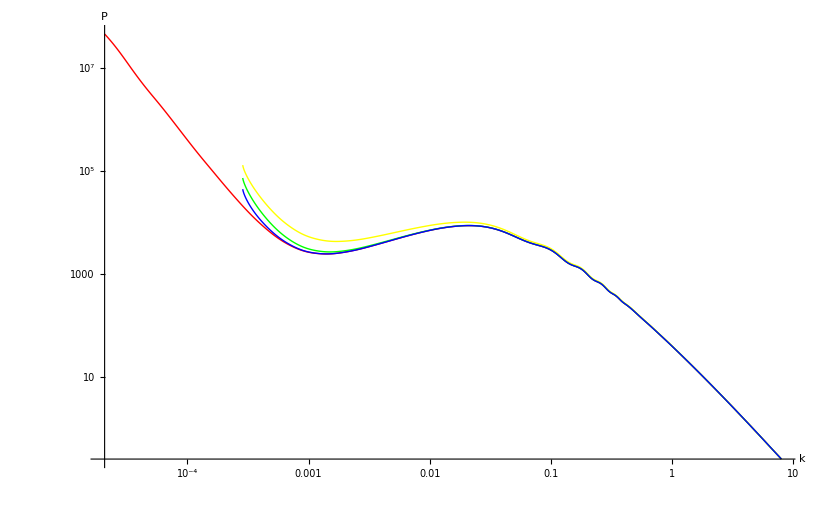

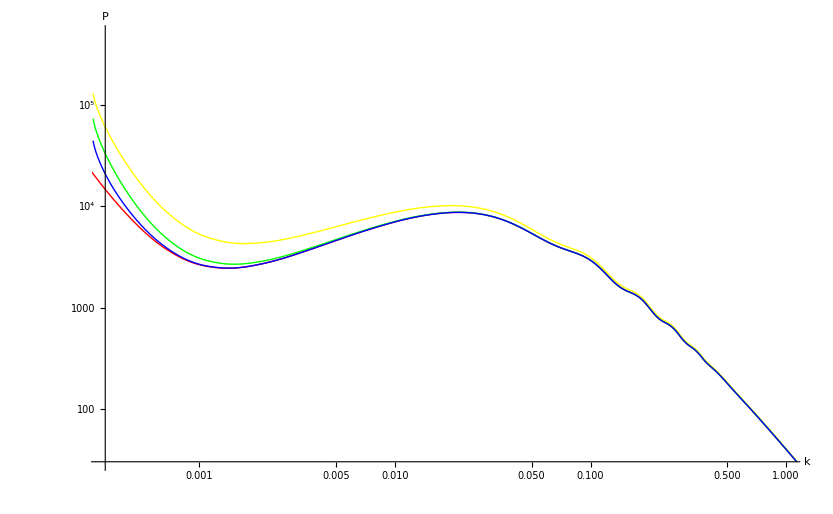

Plot Qfactors vs k

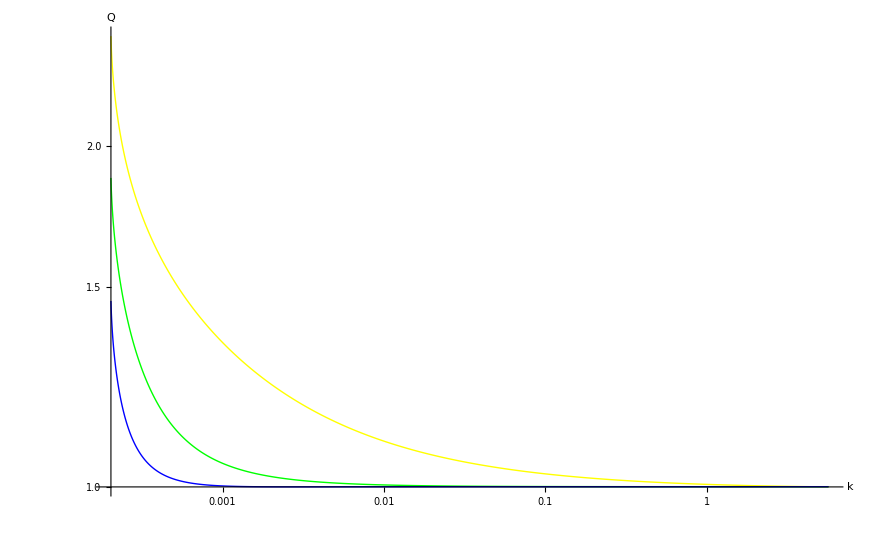

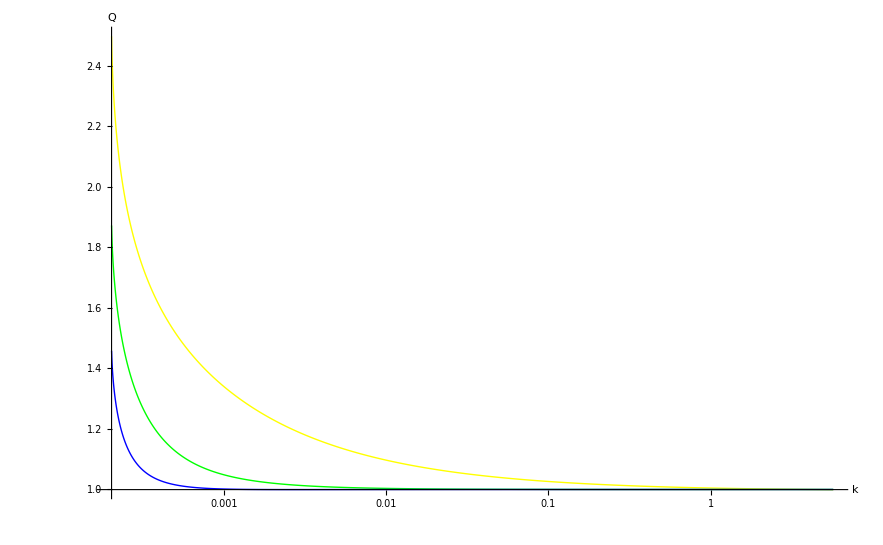

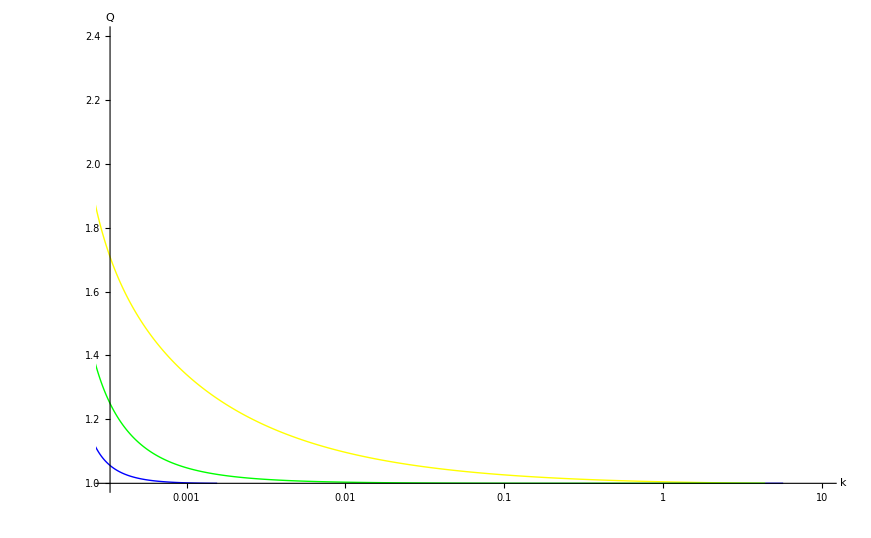

Plot growth factors of a for all models. Normalized.

NIntegrate::nlim: x = a is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.7194}. NIntegrate obtained 41.459  + 55.5417\ ⅈ
 and 38.5744 for the integral and error estimates.

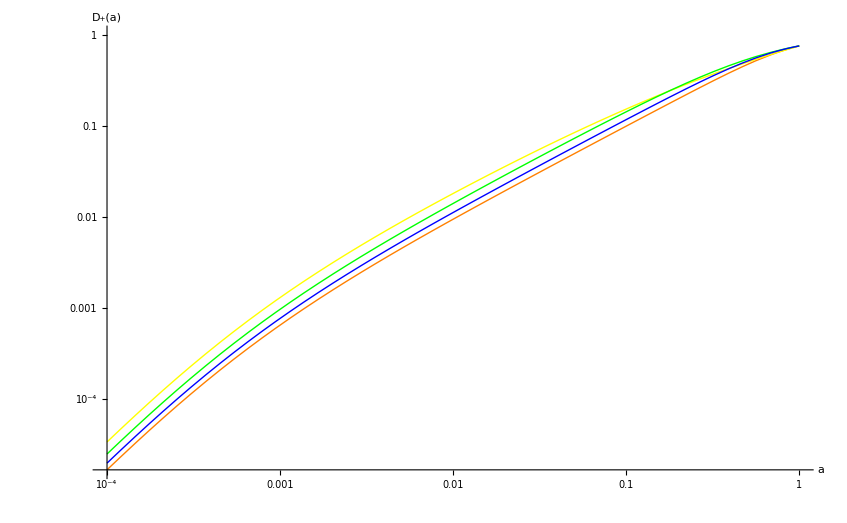

Plot Hubble distances. Normalized.

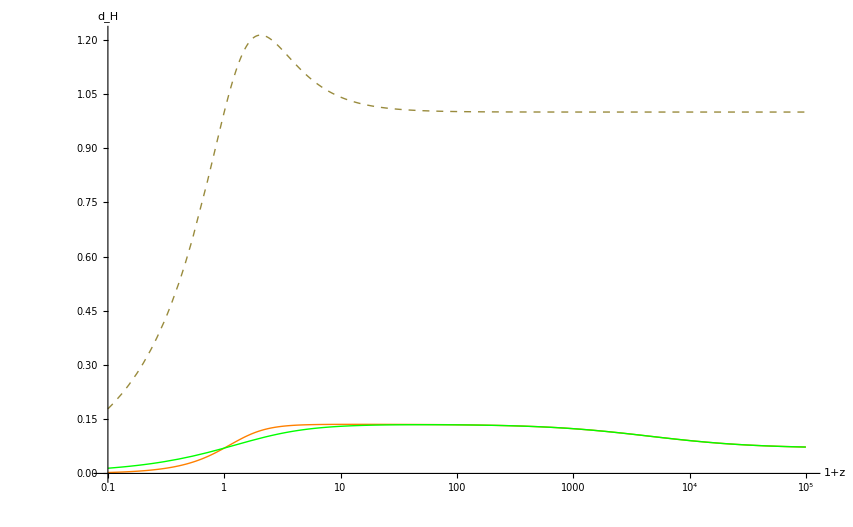

```mathematica
(*********************************************)
Print[Style["Construct the normalized power spectrum (different units) and export them",Orange]]
(*********************************************)
PowerSS=Table[{PowerS[[i,1]]/h,PowerS[[i,2]]  h^3},{i,1,leth}];
Export["E:\\Nutshare\\Store\\Projects\\HZ\\PowerSpectrum\\PowerSpectrum_Notes\\Mathematica\\DEs\\PowerSScale.xls",PowerSS,"XLS"]
PowerSScale=Import["E:\\Nutshare\\Store\\Projects\\HZ\\PowerSpectrum\\PowerSpectrum_Notes\\Mathematica\\DEs\\PowerSScale.xls"];
PowerDE2=Import["E:\\Nutshare\\Store\\Projects\\HZ\\PowerSpectrum\\PowerSpectrum_Notes\\Mathematica\\DEs\\PowerSDE2.xls"];
PowerDE3=Import["E:\\Nutshare\\Store\\Projects\\HZ\\PowerSpectrum\\PowerSpectrum_Notes\\Mathematica\\DEs\\PowerSDE3.xls"];
PowerDE4=Import["E:\\Nutshare\\Store\\Projects\\HZ\\PowerSpectrum\\PowerSpectrum_Notes\\Mathematica\\DEs\\PowerSDE4.xls"];
(*********************************************)
Print[Style["Import the Q factors calculated previously.",Orange]]
(*********************************************)
QfDe2VsL=Import["E:\\Nutshare\\Store\\Projects\\HZ\\PowerSpectrum\\PowerSpectrum_Notes\\Mathematica\\DEs\\QfactorDE2vsL.xls"];
QfDe3VsL=Import["E:\\Nutshare\\Store\\Projects\\HZ\\PowerSpectrum\\PowerSpectrum_Notes\\Mathematica\\DEs\\QfactorDE3vsL.xls"];
QfDe4VsL=Import["E:\\Nutshare\\Store\\Projects\\HZ\\PowerSpectrum\\PowerSpectrum_Notes\\Mathematica\\DEs\\QfactorDE4vsL.xls"];
(*********************************************)
Print[Style["Plot P(k)",Orange]]
(*********************************************)
ListLogLogPlot[{PowerSScale,PowerDE2,PowerDE3,PowerDE4},Joined->True, AxesLabel-> {k,P},PlotRange->Automatic,PlotStyle->{Red,Yellow,Green,Blue}]
ListLogLogPlot[{PowerSScale,PowerDE2,PowerDE3,PowerDE4},Joined->True, AxesLabel-> {k,P},PlotRange->{{3.3*10^-4,1},{30,500000}},PlotStyle->{Red,Yellow,Green,Blue}]
(*********************************************)
Print[Style["Plot Qfactors vs k",Orange]]
(*********************************************)
ListLogLogPlot[{QfDe2VsL,QfDe3VsL,QfDe4VsL},Joined->True, AxesLabel-> {k,Q},PlotRange->Full,PlotStyle->{Yellow,Green,Blue}]
ListLogLinearPlot[{QfDe2VsL,QfDe3VsL,QfDe4VsL},Joined->True, AxesLabel-> {k,Q},PlotRange->Full,PlotStyle->{Yellow,Green,Blue}]
ListLogLinearPlot[{QfDe2VsL,QfDe3VsL,QfDe4VsL},Joined->True, AxesLabel-> {k,Q},PlotRange->{{3.3*10^-4,10},{1,2.4}},PlotStyle->{Yellow,Green,Blue}]
(*Table[NSolve[PowerS[[i,1]]==Subscript[H, 2][Subscript[a, 2]] && Subscript[a, 2]>0,Subscript[a, 2],Reals],{i,1,Length[PowerS]}]*)
(*********************************************)
Print[Style["Plot growth factors of a for all models. Normalized.",Orange]]
(*********************************************)
LogLogPlot[{fracs Subscript[Growth, s][a],GrowthL[a],frac2 Subscript[GrowthDE, 2][a],frac3 Subscript[GrowthDE, 3][a],frac4 Subscript[GrowthDE, 4][a]},{a,10^-4,1},PlotStyle->{Red,Orange,Yellow,Green,Blue},AxesLabel-> {a,"D_+(a)"}]
(*********************************************)
Print[Style["Plot Hubble distances. Normalized.",Orange]]
(*********************************************)
LogLinearPlot[{LambdaL[mn]/Lambdas[mn],Lambda3[mn]/Lambdas[mn],LambdaL[mn]/Lambda3[mn]},{mn,0.1,10^5},PlotStyle->{Orange,Green,Dashed},AxesLabel->{"1+z","d_H"}]
```

## Draft

Use particle horizon

```mathematica
Subscript[w, 1]=-1;
Subscript[w, 2]=-0.5;
Subscript[Ω, DE0]=0.734;
Subscript[Ω, k0]=0;
Subscript[Ω, m0]=0.1334/(0.71^2);
Subscript[Ω, r0]=8.09*10^-5;
Subscript[H, 0]=71/300000;
Subscript[H, 1][a_]:=Subscript[H, 0] √(Subscript[Ω, m0] a^-3+Subscript[Ω, r0] a^-4+Subscript[Ω, DE0] a^(-3(1+Subscript[w, 1])))
Subscript[H, 2][a_]:=Subscript[H, 0] √(Subscript[Ω, m0] a^-3+Subscript[Ω, r0] a^-4+Subscript[Ω, DE0] a^(-3(1+Subscript[w, 2])))
Subscript[d, H,1][a]=1/(Subscript[H, 1][a]);Subscript[d, H,2][a]=1/(Subscript[H, 2][a]);

Subscript[kL, 1][a_]=1/NIntegrate[1/(x^2 Subscript[H, 1][x]),{x,0,a}];Subscript[kL, 2][a_]=1/NIntegrate[1/(x^2 Subscript[H, 2][x]),{x,0,a}];
Subscript[GrowthL, 1][a_]:= 5/2 Subscript[Ω, m0] (Subscript[H, 1][a])/Subscript[H, 0]  NIntegrate[1/(x^3((Subscript[H, 1][x])/Subscript[H, 0])^3),{x,0,a}];
Subscript[GrowthL, 2][a_]:=5/2 Subscript[Ω, m0] (Subscript[H, 2][a])/Subscript[H, 0]  NIntegrate[1/(x^3((Subscript[H, 2][x])/Subscript[H, 0])^3),{x,0,a}];
(*Add some test*)
xyz[mn_]:=Subscript[GrowthL, 1][1/mn];rst[mn_]=Subscript[GrowthL, 2][1/mn];
LogLogPlot[{(mn) xyz[mn],(mn) rst[mn]},{mn,0.1,100}]

LogPlot[{Subscript[kL, 1][a],Subscript[kL, 2][a]},{a,10^-3,1}];
LogLogPlot[{Subscript[GrowthL, 1][a],Subscript[GrowthL, 2][a]},{a,10^-3,1}];
Plot[{(Subscript[GrowthL, 1][1])/(Subscript[GrowthL, 1][a]),(Subscript[GrowthL, 2][1])/(Subscript[GrowthL, 2][a])},{a,10^-3,1}];
```

## Data

datalist

```mathematica
PowerS=Import["E:\\Nutshare\\Store\\Projects\\HZ\\PowerSpectrum\\PowerSpectrum_Notes\\Mathematica\\PSLCDM.dat"];
Table[PowerS[[i,2]],{i,1,Length[PowerS]}]
```

```mathematica
PowerS[[2,1]]
```